### Demo Function

```mathematica
f[x_] := x*Cos[x];
```

```mathematica
Plot[f[x], {x,-1, 5}]
```

```mathematica
Plot[f'[x], {x, -1, 5}]
```

```mathematica
x0 = 2;
```

```mathematica
lf[x_] := f[x0] + f'[x0] * (x-x0);
```

```mathematica
Plot[{f[x], lf[x]}, {x, -1, 5}]
```

### Function 1

```mathematica
f1[x_] := Cos[(x^5-1)/(1+x^3)];
```

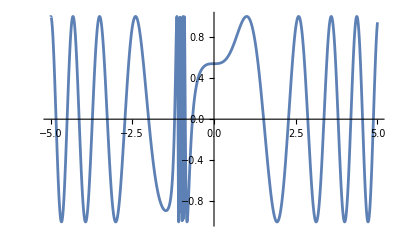

```mathematica
Plot[f1[x], {x, -5, 5}]
```

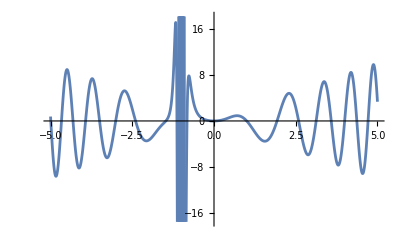

```mathematica
Plot[f1'[x], {x, -5, 5}]
```

```mathematica
x0 = 1.3;
```

```mathematica
lf1[x_] := f[x0] + f1'[x0] * (x-x0);
```

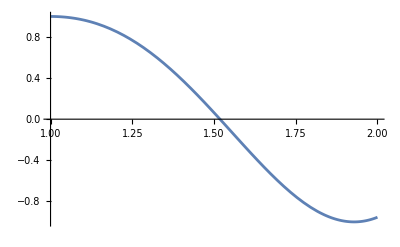

```mathematica
Plot[{f1[x], lf1[x]}, {x, 1, 2}]
```

### Function 2

```mathematica
f2[x_] := Cos[(1-Cos[2x])/(2+Sin[x])^2];
Plot[f2[x], {x, -5, 5}];
```

```mathematica
Plot[f2'[x], {x, -5, 5}];
```

```mathematica
x0 = 2;
```

### Function 3

```mathematica
f3[x_] := Cos[(1-Cos[2x])/(1+Sin[x])^2];
```

### Function 4

```mathematica
f4[x_] := x*Sin[1/x]
```